Interstellar Ring
Ruth Gregory
Aldo Riello
Ifigeneia Giannakoudi

### 3. Null geodesics in a Schwarzschild’s spacetime

```mathematica
Rs= 2;
```

### (a) Define the effective potential Ueff[u , b ]. Plot Ueff[u, b] for b = 4, 3√3, 7 in the range −0.3 < u < 2. What do you notice? Cf. Eq. 6.3.33 of Wald.

```mathematica
(* Define Ueff[u,b] *)
Ueff[u_,b_]:=1/b^2 -u^2 +Rs * u^3
```

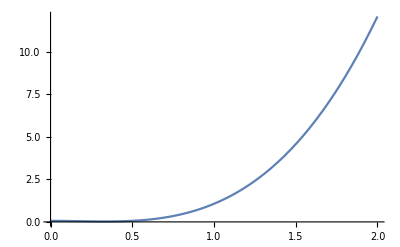

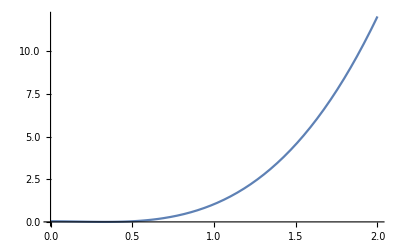

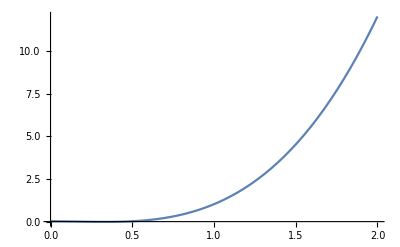

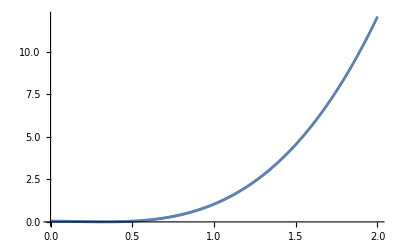

```mathematica
(* Plot Ueff[u,b] for b=4,3√3,7 in the range−0.3<u<2 (seperate plots)*)

p1 = Plot[Ueff[u, 4],{u,0,2}]
p2 = Plot[Ueff[u, 3√3],{u,0,2}]
p3 = Plot[Ueff[u, 7],{u,0,2}]
Show[p1, p2, p3]
```

```mathematica
(* What do you notice? Define bmin *)
bmin = 4
```

### (c) Define r0[b]

```mathematica
(* solve the corresponding equation to find periastron *)
```

```mathematica
r0[b_]=
```

```mathematica
(* Plot here for b in (3,10) *)
```

```mathematica
u0[b_]:= 1/r0[b]
```

### (d) Define the function bcrit[a]

```mathematica
bcrit[a_]:=
```

### (e) Do a Parametric plot of the shape of the geodesic on the plane χ = π/2; use the function psiofu[u , b ] and do the plot for the values b = 4, 3√3, 7. What do you notice for the trajectory associated to b = 3√3?

```mathematica
(* Integrate up to the periastron because then u changes sign*)
psiofu[u_,b_] :=
```

```mathematica
(* 3 Different Plots here *)
```

```mathematica
(* Parametric Plot for b = (3 √3 *)
```

### (f) Define two functions Psi[b ,a ] and Psiplus[b ,a ] corresponding to the two branches of the partial deflection angle Δψ_ϕ as parametrized by the initial radial position and the final impact parameter of the geodesics labelled by φ. Fix a = 6 and plot these two branches in a unique graph where Y = Δψ_ϕ and X = b

```mathematica
Psi[b_,a_]:=
```

```mathematica
Psiplus[b_,a_]:=
```

```mathematica
(* Plot together for a=6 *)
```

### 4. Observer’s frame

```mathematica
Theta[phi_,theta0_] :=
```

```mathematica
(* Plot for theta0=π/3 *)
```

### 5. Drawing the observed disk

```mathematica
(* Plot for Psi and Psiplus again for a = 6 *)
```

```mathematica
(* find and set the value of the impact parameter where the branches seperate*)
bamax =
```

We will reverse the function ψ(b) numerically. So, we will work with the 2 branches separately.

```mathematica
(* We set a discrete grid of values for Psi[b,6] for values of b from bmin to bmax with a step of 0.01 for the first branch. The values of Psi are saved in the first line and the corresponding b values in the second line. We will do the same for the second branch and then we can 'reverse' the function in the sense that we know the Psi's corresponding to b's but the table can also give the b's corresponding to Psi's, which is single valued. *)
psi1 = Table[{Psi[b,6],b},{b,bmin, bmax, 0.01}];
```

```mathematica
(* We set a deiscrete grid of values for Psi[b,6] for values of b from bmin+0.2 (for numerical reasons) to bmax with a step of 0.01 for the second branch, and then reverse the table because the function is descending *)
psi2 = Reverse[Table[{Re[Psiplus[b,6]],b},{b,bmin+0.006, bmax, 0.01}]];
```

```mathematica
(* We join the two branches, so with these points we could recreate Psi[b,6]*)
fullpsi = Join[psi1,psi2];
```

```mathematica
(* We join the two branches, so with these points we could recreate Psi[b,6]*)
x = fullpsi[[All,2]];
y = fullpsi[[All,1]]/Pi;
ListPlot[Transpose[{x,y}],PlotRange-> {0,3}]
```

If everything is going well, this plot should resemble the initial analytic plot in the beginning of this section.

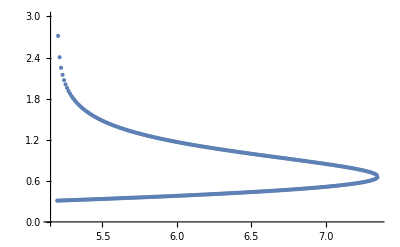

```mathematica
(* We use interpolation now to find b(Psi), essentially we use the pairs (Psi,b) of the fullpsi table and we interpolate the analytic form of the function. We end up with the desired b(Psi).*)
bofpsi = Interpolation[fullpsi] (* this works like a function *)
bofpsi[Pi] (* the result should be around 6.48*)
```

InterpolatingFunction[…]

6.4816

```mathematica
(* We found b(Psi), but we want b(phi). We know that Psi[b,6]= Theta[phi,theta0], so to find b[phi], we will find the b[Theta[phi,theta0]]*)
Impact[phi_,theta0_]:=
```

```mathematica
(* Plot Impact for theta0=Pi/3 *)
```

```mathematica
(* Use ParametricPlot to plot the rings for theta0=Pi/3 , 0.4Pi and 0.45 Pi *)
```